```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
ClearAll[A1];
A1=1/u(-((18 m u+9 u^2+4 m^2 (2+3 u^3)) Derivative[0,1][f][m,u])+(27 u^2-64 m^3 u^2-128 m^4 u^4-24 m^2 (-1+6 u^3)+m (52 u-108 u^4)) (2 Derivative[0,1][f][m,u]+u Derivative[0,2][f][m,u])-(8 m+9 u) (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4) (6 Derivative[0,1][f][m,u]+u (6 Derivative[0,2][f][m,u]+u Derivative[0,3][f][m,u])));
```

```mathematica
A2 = Simplify[A1/.{f->Function[{m,u},ff[m^3,u/m]]}/.{m->l^(1/3),u->U l^(1/3)}]
```

-((8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5) ff^(0,1)[l,U])/U+(-24-50 U+(-27+320 l) U^2+2016 l U^3+4 (783-224 l) l U^4-54 l (-27+16 l) U^5) ff^(0,2)[l,U]-U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) ff^(0,3)[l,U]

```mathematica
Coefficient[A2, {Derivative[0,3][ff][l,U],Derivative[0,2][ff][l,U],Derivative[0,1][ff][l,U]}]
```

{-U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4),-24-50 U+(-27+320 l) U^2+2016 l U^3+4 (783-224 l) l U^4-54 l (-27+16 l) U^5,-(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/U}

```mathematica
D4[l_,U_]:=1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4;
Q4[l_,U_]:=1-8l U^2-24U^3+16l^2U^4;
Q6[l_,U_]:=1-12U^2l-36U^3l+48U^4l^2+144U^5l^2+U^6l^2(216-64l);
```

```mathematica
A3=Simplify[A2/.ff->Function[{l,U},Integrate[a[l,U]/U, U]]]
```

2 l (32+282 U-6 (-81+32 l) U^2-9 (-27+16 l) U^3) a[l,U]+((-8-16 U+3 (-3+64 l) U^2+1296 l U^3+4 (513-160 l) l U^4+36 (27-16 l) l U^5) a^(0,1)[l,U])/U-(8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) a^(0,2)[l,U]

```mathematica
{a2,a1,a0}=Simplify[Coefficient[A3,{Derivative[0,2][a][l,U],Derivative[0,1][a][l,U],a[l,U]}]]
```

{-((8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)),-16-8/U+3 (-3+64 l) U+1296 l U^2+4 (513-160 l) l U^3+36 (27-16 l) l U^4,2 l (32+282 U-6 (-81+32 l) U^2-9 (-27+16 l) U^3)}

```mathematica
P[l_,U_]=Together[a1/a2]
```

(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4))

```mathematica
Q[l_,U_]=Together[a0/a2]
```

(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4))

```mathematica
matA[l_,U_]:={{0, 1}, {-Q[l,U], -P[l, U]}};
```

```mathematica
A4=Simplify[A3/a2]
```

(2 l U (-32-282 U+6 (-81+32 l) U^2+9 (-27+16 l) U^3) a[l,U]+(8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5) a^(0,1)[l,U]+U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) a^(0,2)[l,U])/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

```mathematica
Simplify[A4/.{a->Function[{l,U},U^r(1+b1 U+b2 U^2)]}]
Simplify[Series[%,{U,0,2}]]
```

(U^(-2+r) (2 l U^2 (1+b1 U+b2 U^2) (-32-282 U+6 (-81+32 l) U^2+9 (-27+16 l) U^3)+(8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5) (U (b1+2 b2 U)+r (1+b1 U+b2 U^2))+(8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) (2 b2 U^2+r^2 (1+b1 U+b2 U^2)+r (-1+b1 U+3 b2 U^2))))/((8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

U^r (r^2/U^2+(-r/8+b1 (1+r)^2)/U+(-8 l+(17 r)/64-16 l r-1/8 b1 (1+r)+b2 (2+r)^2)+O[U]^1)

```mathematica
Simplify[A4/.{a->Function[{l,U},(U+8/9)^r(1+b1 (U+8/9)+b2 (U+8/9)^2)]}]
Simplify[Series[%,{U,-8/9,1}]]
```

((8/9+U)^r (-18 l U (8+9 U) (32+282 U-6 (-81+32 l) U^2-9 (-27+16 l) U^3) (1+b1 (8/9+U)+b2 (8/9+U)^2)+(8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5) (81 r+9 b1 (1+r) (8+9 U)+b2 (2+r) (8+9 U)^2)+9 U (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) (b2 (2+3 r+r^2) (8+9 U)^2+9 r (9 (-1+r)+b1 (1+r) (8+9 U)))))/(9 U (8+9 U)^2 (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

(8/9+U)^r (((-2+r) r)/(U+8/9)^2+(b1 (-1+r^2)+(9 (189 r-256 l (-1+5 r)))/(8 (27+256 l)))/(U+8/9)+1/(64 (27+256 l)^2)(65536 l^2 (324+(-405+128 b2) r+64 b2 r^2)+6912 l (-567+2 (81+128 b2) r+128 b2 r^2)+729 r (-5265+64 b2 (2+r))-72 b1 (27+256 l) (-189 (1+r)+256 l (4+5 r)))-1/(512 (27+256 l)^3)9 (72 b1 (27+256 l) (47385 (1+r)-6912 l (-5+2 r)+65536 l^2 (1+5 r))+64 b2 (27+256 l)^2 (-189 (2+r)+256 l (9+5 r))+81 (-10058013 r+16777216 l^3 (-7+5 r)+5308416 l^2 (3+5 r)-186624 l (80+69 r))) (U+8/9)+O[U+8/9]^2)

```mathematica
l0=1;
```

```mathematica
U0=U/.Simplify[Solve[1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4==0/.{l->l0},U]]
```

{,,,}

```mathematica
Simplify[A4/.{a->Function[{l,U},(U-U0[[4]])^r]}]
Simplify[Series[%,{U,U0[[4]],0}]]
```

((2 l U (-32-282 U+6 (-81+32 l) U^2+9 (-27+16 l) U^3)+((-1+r) r U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))/((U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)+(r (8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5))/(U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)) (U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^r)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

(U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^r (((-1+r) r)/((U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)+(r (8+16 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+9 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+64 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4 (10+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)-12 l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (16+108 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+171 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+81 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3)))/(Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044 (8+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044) (1+Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+16 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4-l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+36 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+27 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)) (U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044))+(2 l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044) (-32-314 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044-768 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2-729 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3-243 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+768 l^3 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^6 (4+3 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)-32 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4 (64+393 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+567 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+243 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3)+l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (448+3744 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+15048 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+27054 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+21870 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+6561 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^5))-r (64+272 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+416 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+288 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+81 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+1024 l^4 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^8 (80+180 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+81 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)-128 l^3 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^6 (256+2880 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+7506 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+7047 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+2187 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4)+4 l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3 (1792+7524 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+12042 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+8505 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+2187 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4)+4 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4 (512+28288 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+156528 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+364176 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+425736 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+249318 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^5+59049 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^6)))/((Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (1+Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+16 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4-l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+36 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+27 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2))^2)+O[U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044]^1)

```mathematica
upath[t_]:=1/10 Exp[2Pi I t];
```

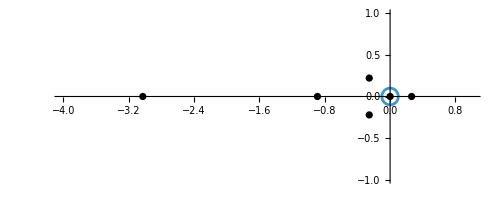

```mathematica
Show[
ParametricPlot[ReIm[upath[t]],{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@Join[U0,{0,-8/9}]]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==upath'[t]*matA[l0,upath[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,2}]
```

{{Psi→InterpolatingFunction[…]}}

```mathematica
Mon=Chop[Psi[1]/.First[sol]]
```

{{1.-0.368208 ⅈ,1.20398×10^-9+0.585934 ⅈ},{-1.61028×10^-7-0.231386 ⅈ,1.+0.368208 ⅈ}}

```mathematica
Pi1=Series[1+c[1]U+c[2] U^2+c[3] U^3+c[4] U^4+c[5] U^5+c[6] U^6,{U,0,6}];
Pi2=Pi1 Log[U]+b[1]U+b[2] U^2+b[3] U^3+b[4] U^4+b[5] U^5+b[6] U^6;
```

```mathematica
A5[f_,U_]:=(2 U (-32-282 U-294 U^2-99 U^3) f+(8+16 U-183 U^2-1296 U^3-1412 U^4-396 U^5) D[f,U]+U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4) D[f,{U,2}])/(U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4));
```

```mathematica
sol1=Solve[Simplify[Series[A5[Pi1,U], {U,0,6}]]==0, Array[c,6]]
```

{{c[1]→0,c[2]→2,c[3]→6,c[4]→6,c[5]→60,c[6]→110}}

```mathematica
sol2=Solve[Simplify[Series[A5[Pi2/.First[sol1],U], {U,0,6}]]==0,Array[b,6]]
```

{{b[1]→1/8,b[2]→31/16,b[3]→139/24,b[4]→279/32,b[5]→7843/120,b[6]→400/3}}

```mathematica
{sPi1,sPi2}={Pi1,Pi2}/.First[sol1]/.First[sol2]
```

{1+2 U^2+6 U^3+6 U^4+60 U^5+110 U^6+O[U]^7,Log[U]+U/8+1/16 (31+32 Log[U]) U^2+1/24 (139+144 Log[U]) U^3+3/32 (93+64 Log[U]) U^4+1/120 (7843+7200 Log[U]) U^5+10/3 (40+33 Log[U]) U^6+O[U]^7}

```mathematica
A5[#,U]&/@{sPi1,sPi2}
```

{O[U]^5,O[U]^5}

```mathematica
Cmat=Normal[{{sPi1,sPi2},{D[sPi1,U],D[sPi2,U]}}]/.{U->upath[0]}
```

{{102731/100000,1/80+(7843-7200 Log[10])/12000000+(139-144 Log[10])/24000+(3 (93-64 Log[10]))/320000+(40-33 Log[10])/300000+(31-32 Log[10])/1600-Log[10]},{3203/5000,81/8+(9283-7200 Log[10])/240000+1/800 (187-144 Log[10])+(91-66 Log[10])/10000+(3 (109-64 Log[10]))/8000+1/80 (47-32 Log[10])}}

```mathematica
Cmat=Normal[{{sPi1/(2 Pi I),-2 sPi2/Pi^2 + m sPi1/(2 Pi I)},{D[sPi1,U]/(2 Pi I),-2 D[sPi2,U]/Pi^2 + m D[sPi1,U]/(2 Pi I)}}]/.{U->upath[0]}/.{m->1/3Log[l0]/(2Pi I)}
```

{{-(102731 ⅈ)/(200000 π),-1/(40 π^2)-(7843-7200 Log[10])/(6000000 π^2)-(139-144 Log[10])/(12000 π^2)-(3 (93-64 Log[10]))/(160000 π^2)-(40-33 Log[10])/(150000 π^2)-(31-32 Log[10])/(800 π^2)+(2 Log[10])/π^2},{-(3203 ⅈ)/(10000 π),-81/(4 π^2)-(9283-7200 Log[10])/(120000 π^2)-(187-144 Log[10])/(400 π^2)-(91-66 Log[10])/(5000 π^2)-(3 (109-64 Log[10]))/(4000 π^2)-(47-32 Log[10])/(40 π^2)}}

```mathematica
Inverse[Cmat].Mon.Cmat//MatrixForm
```

(1.-0.00283997 ⅈ | 8.01212-8.15122×10^-9 ⅈ
1.00799×10^-6-1.37023×10^-8 ⅈ | 1.+0.00283986 ⅈ)

```mathematica
2Pi I//N
```

0.+6.28319 ⅈ

#### the other points

```mathematica
U0
```

{,,,}

```mathematica
upath[t_]:=U0[[2]]+1/10 Exp[2Pi I t];
```

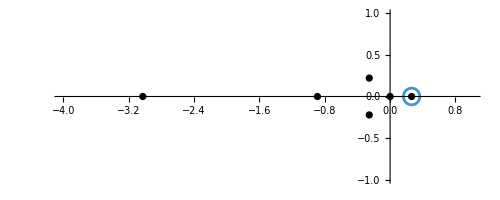

```mathematica
Show[
ParametricPlot[ReIm[upath[t]],{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@Join[U0,{0,-8/9}]]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==upath'[t]*matA[l0,upath[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,2}]
```

{{Psi→InterpolatingFunction[…]}}

```mathematica
Mon=Chop[Psi[1]/.First[sol]]
```

{{1.+1.3074 ⅈ,-3.25347×10^-8+0.760449 ⅈ},{1.21613×10^-7-2.24775 ⅈ,1.-1.3074 ⅈ}}

```mathematica
Series[P[l0,U],{U,U0[[2]],1}]//N
```

1/(U-0.263185)+6.49834-18.126 (U-0.263185)+O[U-0.263185]^2

```mathematica
Series[Q[l0,U],{U,U0[[2]],1}]//N
```

2.15458/(U-0.263185)-1.88023-1.0056 (U-0.263185)+O[U-0.263185]^2

```mathematica
A4/.{a->Function[{l,U}, aa[U]]}/.{l->l0}/.{aa->Function[U,(U-U0[[2]])^r]}
Series[%, {U,U0[[2]],2}]//N
```

((-1+r) r U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4) (U-)^(-2+r)+r (8+16 U-183 U^2-1296 U^3-1412 U^4-396 U^5) (U-)^(-1+r)+2 U (-32-282 U-294 U^2-99 U^3) (U-)^r)/(U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4))

(-0.263185+U)^(-2.+r) ((-1.+r) r+O[U-0.263185]^1)+(-0.263185+U)^r (2.15458/(U-0.263185)-1.88023+O[U-0.263185]^1)+(-0.263185+U)^(-1.+r) (r/(U-0.263185)+6.49834 r+O[U-0.263185]^1)

```mathematica
Pi1=Series[1+c[1](U-U0[[2]])+c[2] (U-U0[[2]])^2+c[3] (U-U0[[2]])^3,{U,U0[[2]],3}];
Pi2=Pi1 Log[U-U0[[2]]]+b[1](U-U0[[2]])+b[2] (U-U0[[2]])^2+b[3] (U-U0[[2]])^3;
Pi3=Series[(U-U0[[2]])+b[2] (U-U0[[2]])^2+b[3] (U-U0[[2]])^3+b[4] (U-U0[[2]])^4,{U,U0[[2]],4}];
```

```mathematica
A4/.{l->l0}/.{a->Function[{l,U},Pi1]}//N//Simplify
```

2.15458/(U-0.263185)+(-1.88023+2.15458 c[1.])+(-1.0056-1.88023 c[1.]+2.15458 c[2.]) (U-0.263185)+(9.92163-1.0056 c[1.]-1.88023 c[2.]+2.15458 c[3.]) (U-0.263185)^2+O[U-0.263185]^3

```mathematica
A5[f_,U_]:=(2 U (-32-282 U-294 U^2-99 U^3) f+(8+16 U-183 U^2-1296 U^3-1412 U^4-396 U^5) D[f,U]+U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4) D[f,{U,2}])/(U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4));
```

```mathematica
sol1=Simplify@Solve[Simplify[Series[A5[Pi1,U], {U,U0[[2]],3}]]==0, Array[c,3]];
```

```mathematica
sol2=Simplify@Solve[Simplify[Series[A5[Pi2/.First[sol1],U], {U,U0[[2]],3}]]==0,Array[b,3]];
```

Series::ztest1: Unable to decide whether numeric quantity -28/11-336/121 Root[-1331-121 #1+88 Slot[«1»]^2+36 Slot[«1»]^3+#1^4&,2,0]-(1481 Root[«1»&,2,0]^2)/1331-(6912 («1»)^3)/14641-8 Root[«1»&,2,0]+119 Root[«1»&,2,0]^2+1008 Root[«5»+11 Power[«2»]&,2,0]^3+1324 Root[-1-Slot[«1»]+8 Power[«2»]+36 Power[«2»]+11 Power[«2»]&,2,0]^4+396 Root[-1-Slot[«1»]+8 Power[«2»]+36 Power[«2»]+11 Power[«2»]&,2,0]^5 is equal to zero. Assuming it is.

```mathematica
{sPi1,sPi2}={Pi1,Pi2}/.First[sol1]/.First[sol2];
```

```mathematica
Cmat=Normal[{{sPi1,sPi2},{D[sPi1,U],D[sPi2,U]}}]/.{U->upath[0]}
```

```mathematica
Inverse[Cmat].Mon.Cmat//MatrixForm
```

(1.-0.00283997 ⅈ | 6.40195×10^-9+6.29271 ⅈ
-1.74463×10^-8-1.28341×10^-6 ⅈ | 1.+0.00283986 ⅈ)

```mathematica
2Pi I//N
```

0.+6.28319 ⅈ

```mathematica
(* 
Pi1 -> 1 + ...;
Pi2 -> Log[U] Pi1 + ...;
om1 -> Log[U] + ...;
om2 -> Log[U]^2/2 + ...;

T   -> Log[U]/(2 Pi I) = om1/(2 Pi I);
TD  -> -Log[U]^2/Pi^2  = -2 om2/Pi^2 -(ⅈ m om1)/(2 π)-m^2/2;

a   -> Pi1/(2 Pi I);
aD  -> -2 Pi2/Pi^2 + m Pi1/(2 Pi I);
*)
```

```mathematica
{ppp1,(Log[U] ppp1+b[1] U+b[2] U^2+b[3] U^3)}/U /.{ppp1->1+a[1] U+a[2] U^2+a[3] U^3}//Expand
Series[Integrate[%,U],{U,0,2}]
```

{1/U+a[1]+U a[2]+U^2 a[3],b[1]+U b[2]+U^2 b[3]+Log[U]/U+a[1] Log[U]+U a[2] Log[U]+U^2 a[3] Log[U]}

{Log[U]+a[1] U+1/2 a[2] U^2+O[U]^3,Log[U]^2/2+(-a[1]+b[1]+a[1] Log[U]) U+1/4 (-a[2]+2 b[2]+2 a[2] Log[U]) U^2+O[U]^3}

```mathematica
Integrate[Log[U]/U,U]
```

Log[U]^2/2

```mathematica
Integrate[Log[U],U]
```

-U+U Log[U]

```mathematica
Integrate[Log[U]U^n,U]
```

(U^(1+n) (-1+(1+n) Log[U]))/(1+n)^2

```mathematica
ZLV[{-1,0,0,0},Log[U]/(2 Pi I),m]
```

-m^2/2-(ⅈ m Log[U])/(2 π)-Log[U]^2/π^2

```mathematica
Solve[Log[U]^2/2==om2,Log[U]]
-Log[U]^2/π^2/.First[%]
```

{{Log[U]→-√2 √om2},{Log[U]→√2 √om2}}

-(2 om2)/π^2

1.4

```mathematica
u0=Truncate;
Series[2Sqrt[2]/(U^2-2),{U,1.414213562373095,1}]
```

-6.36905×10^15-4.05648×10^31 (U-1.41421)+O[U-1.41421]^2

```mathematica
FullForm[u0]
```

1.

## redo

```mathematica
P[l_,U_]:=(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
Q[l_,U_]:=(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
PF[f_,l_,U_]:=D[f,{U,2}] + D[f, {U,1}]P[l,U] + f Q[l, U];
matA[l_,U_]={{0, 1}, {-Q[l,U], -P[l, U]}};
```

```mathematica
l0=1;
```

```mathematica
U0=Join[U/.Simplify[Solve[1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4==0/.{l->l0},U]], {-8/9,0}]
```

{,,,,-8/9,0}

```mathematica
UPath6[t_]:=U0[[6]]+1/10Exp[2Pi I t];
UPath2[t_]:=U0[[2]]+Abs[U0[[2]]-UPath6[0]]Exp[2Pi I (t+1/2)];
UPath4[t_]:=U0[[4]]+2/10Exp[2Pi I t];
UPath3[t_]:=U0[[3]]+2/10Exp[2Pi I t];
```

```mathematica
UPath6To2[t_]:=(1-t)UPath6[0]+t UPath2[1/2]
```

```mathematica
UPathB[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[5]]+I/10}, {3/4,U0[[5]]-I/10}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

```mathematica
UPath1[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[1]]+I/5+1/3}, {3/4,U0[[1]]-I/5+1/3}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

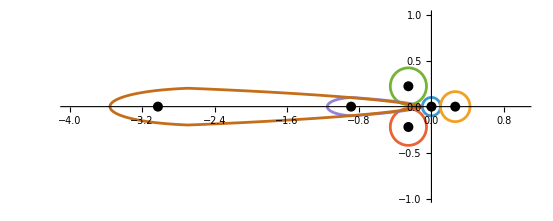

```mathematica
Show[
ParametricPlot[{ReIm[UPath6[t]], ReIm[UPath2[t]], ReIm[UPath4[t]],ReIm[UPath3[t]],ReIm[UPathB[t]],ReIm[UPath1[t]]},{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@U0]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6'[t]*matA[l0,UPath6[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->60];
Mon6=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath2'[t]*matA[l0,UPath2[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50];
Mon2=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath4'[t]*matA[l0,UPath4[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50];
Mon4=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath3'[t]*matA[l0,UPath3[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50];
Mon3=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPathB'[t]*matA[l0,UPathB[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50,MaxSteps->100000];
MonB=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath1'[t]*matA[l0,UPath1[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50,MaxSteps->100000];
Mon1=Psi[1]/.First[sol];
```

```mathematica
Simplify[Series[PF[U^r(1+Sum[a[i](U-U0[[6]])^i,{i,1,2}]),l0,U],{U,U0[[6]],2}]];
```

```mathematica
NumTerms=40;
```

```mathematica
Pi1=(1+Sum[a[i](U-U0[[6]])^i,{i,1,NumTerms}]);
```

```mathematica
Simplify[Series[PF[Pi1,l0,U],{U,U0[[6]],NumTerms}]];
sol=Solve[Thread[%[[3]][[1;;NumTerms]]==0],Array[a,NumTerms]];
Pi1Sol=Pi1/.First[sol];
```

```mathematica
Pi2=Pi1Sol Log[U-U0[[6]]]+Sum[b[i](U-U0[[6]])^i,{i,1,NumTerms}];
```

```mathematica
Simplify[Series[PF[Pi2,l0,U],{U,U0[[6]],NumTerms}]];
sol=Solve[Thread[%[[3]][[1;;NumTerms]]==0],Array[b,NumTerms]];
Pi2Sol=Pi2/.First[sol];
```

```mathematica
(* 
Pi1 -> 1 + ...;
Pi2 -> Log[U] Pi1 + ...;
om1 -> Log[U] + ...;
om2 -> Log[U]^2/2 + ...;

T   -> (Log[U] + 1/3 Log[l])/(2 Pi I) = om1/(2 Pi I) + 1/3Log[l]/(2 Pi I);
TD  -> -Log[U]^2/Pi^2  = -2 om2/Pi^2 -(3 Log[l] om1)/(4 π^2)-Log[l]^2/(8 π^2);

a   -> Pi1/(2 Pi I);
aD  -> -2 Pi2/Pi^2 -(3 Log[l] Pi1)/(4 π^2);
*)
```

```mathematica
PiVec={Pi1Sol/(2 Pi I), -2 Pi2Sol/Pi^2 -(3 Log[l0] Pi1Sol)/(4 π^2)};
```

```mathematica
Cmat6={PiVec,D[PiVec,U]}/.{U->UPath6[0]}
```

{{-(51368826850355454276413201770640727189 ⅈ)/(100000000000000000000000000000000000000 π),-(2 (165135901536864897980359448500996868603722075233951269/4190534476128000000000000000000000000000000000000000000-(51368826850355454276413201770640727189 Log[10])/50000000000000000000000000000000000000))/π^2},{-(1614039884510962922005717358443899597 ⅈ)/(5000000000000000000000000000000000000 π),-(2 (3933004942968408341758083281069305437633977031138793423/356195430470880000000000000000000000000000000000000000-(1614039884510962922005717358443899597 Log[10])/2500000000000000000000000000000000000))/π^2}}

```mathematica
N@LinearSolve[Cmat6, Mon6.Cmat6]//MatrixForm
Round[%]//MatrixForm
```

(1.-1.56935×10^-17 ⅈ | 8.+1.5178×10^-28 ⅈ
-5.53501×10^-30-3.35971×10^-30 ⅈ | 1.+1.56935×10^-17 ⅈ)

(1 | 8
0 | 1)

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6To2'[t]*matA[l0,UPath6To2[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->60]
Conn=Psi[1]/.First[sol]
```

{{Psi→InterpolatingFunction[…]}}

{{1.0315995224665550921478831853292808350686725957779372180614,0.055528452411420516203466813327248178299884528167490231375882},{1.1034421104727142975020378671803822305396047151053495983008,0.84978863324912869297157623916939705767930041265184080532164}}

```mathematica
N@LinearSolve[Cmat6, Mon6.Cmat6]//MatrixForm
```

(1.-3.94391×10^-9 ⅈ | 8.+1.5178×10^-28 ⅈ
1.94431×10^-18-3.35971×10^-30 ⅈ | 1.+3.94391×10^-9 ⅈ)

```mathematica
N@LinearSolve[Cmat6, Mon2.Cmat6]//MatrixForm
Round[%]
```

(1.-1.79063×10^-9 ⅈ | -3.2064×10^-18-4.4706×10^-23 ⅈ
-1.-2.18604×10^-24 ⅈ | 1.+1.79063×10^-9 ⅈ)

{{1,0},{-1,1}}

```mathematica
{{1,0},{-1,1}}
{Det[%],Tr[%]}
```

{{1,0},{-1,1}}

{1,2}

```mathematica
Cmat4={PiVec,D[PiVec,U]}/.{U->UPath4[0]};
```

```mathematica
N@LinearSolve[Cmat4, Mon4.Cmat4]//MatrixForm
Round[%]
{Det[%],Tr[%],%ᵀ.{{0,1},{-1,0}}.%}
```

(4.02354-0.0562567 ⅈ | 9.07884-0.126807 ⅈ
-1.00691+0.0234066 ⅈ | -2.02354+0.0562567 ⅈ)

{{4,9},{-1,-2}}

{1,2,{{0,1},{-1,0}}}

```mathematica
Cmat3={PiVec,D[PiVec,U]}/.{U->UPath3[0]};
```

```mathematica
N@LinearSolve[Cmat3, Mon3.Cmat3]//MatrixForm
Round[%]
{Det[%],Tr[%],%ᵀ.{{0,1},{-1,0}}.%}
```

(-2.02354-0.0562567 ⅈ | 9.07884+0.126807 ⅈ
-1.00691-0.0234066 ⅈ | 4.02354+0.0562567 ⅈ)

{{-2,9},{-1,4}}

{1,2,{{0,1},{-1,0}}}

```mathematica
CmatB={PiVec,D[PiVec,U]}/.{U->UPath6[1/2]};
```

```mathematica
N@LinearSolve[CmatB, MonB.CmatB]//MatrixForm
Round[%]
```

(1.+9.99978×10^-22 ⅈ | 8.88327×10^-21+3.89701×10^-21 ⅈ
-4.76884×10^-22-1.14142×10^-22 ⅈ | 1.-3.1749×10^-22 ⅈ)

{{1,0},{0,1}}

```mathematica
N@LinearSolve[CmatB, Mon1.CmatB]//MatrixForm
Round[%]
```

(1.+9.50416×10^-19 ⅈ | 1.+7.60135×10^-18 ⅈ
2.33055×10^-22-3.36565×10^-22 ⅈ | 1.-9.50464×10^-19 ⅈ)

{{1,1},{0,1}}

```mathematica
ComplexExpand[Re[Exp[-I psi]Z],Z]
```

Cos[psi] Re[Z]+Im[Z] Sin[psi]

```mathematica
{r,dF,dB,ch2}.Sigma.{1,m,t,td}
```

-ch2+(-dB+dF) m+(dB+2 dF) t-r td

## Monodromies of T and TD

```mathematica
P[l_,U_]:=(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
Q[l_,U_]:=(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
PF[f_,l_,U_]:=D[f,{U,2}] + D[f, {U,1}]P[l,U] + f Q[l, U]
```

```mathematica
Simplify[PF[U D[f[l,U],U],l,U]]
{cf3,cf2,cf1}=Coefficient[%, {Derivative[0,3][f][l,U],Derivative[0,2][f][l,U],Derivative[0,1][f][l,U]}]
```

((8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5) f^(0,1)[l,U]+U ((24+50 U+(27-320 l) U^2-2016 l U^3+4 l (-783+224 l) U^4+54 l (-27+16 l) U^5) f^(0,2)[l,U]+U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) f^(0,3)[l,U]))/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

{(8 U^2+17 U^3+9 U^4-64 l U^4-360 l U^5-540 l U^6+128 l^2 U^6-243 l U^7+144 l^2 U^7)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)),(24 U+50 U^2+27 U^3-320 l U^3-2016 l U^4-3132 l U^5+896 l^2 U^5-1458 l U^6+864 l^2 U^6)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)),(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))}

```mathematica
FullSimplify[cf2/cf3]
```

3/U-9/(8+9 U)+(1+64 l^2 U^3-4 l U (4+27 U (1+U)))/(1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)

```mathematica
Simplify[cf1/cf3]
```

(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/(U^2 (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

```mathematica
P1[l_,U_]:=3/U-9/(8+9 U)+(1+64 l^2 U^3-4 l U (4+27 U (1+U)))/(1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4);
Q1[l_,U_]:=(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/(U^2 (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4));
```

```mathematica
PF1[f_,l_,U_]:=D[f,{U,3}] + D[f, {U,2}]P1[l,U] + D[f,U]* Q1[l, U];
matA1[l_,U_]:={{0,1,0},{0,0,1},{0,-Q1[l,U],-P1[l,U]}};
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6'[t]*matA1[l0,UPath6[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->60];
Non6=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPathB'[t]*matA1[l0,UPathB[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->50];
NonB=Psi[1]/.First[sol];
```

```mathematica
PiVec1=Join[{1},Simplify[Integrate[PiVec/U,U]+{1/3Log[l0]/(2 Pi I), -Log[l0]^2/(8 π^2)}]];
```

```mathematica
Dmat6={PiVec1,D[PiVec1,U],D[PiVec1,{U,2}]}/.{U->UPath6[0]};
```

```mathematica
LinearSolve[Dmat6, Non6.Dmat6]
Round[%]ᵀ//MatrixForm
```

{{1.,0.999999999999999994280141173144113598618336350310506372029-7.846755432534487665487549292667218495224×10^-18 ⅈ,4.00000000000000000966436998775683750134564047975805205367-1.532829914134107293003058545310885197595×10^-17 ⅈ},{0,1.00000000000000000000000000139641615828765744744770369037-1.5693510864383899412094015847014583678561×10^-17 ⅈ,8.00000000000000006508761059675406004445207851551120215751-1.10254061879683056146788101547×10^-27 ⅈ},{0,1.18022198320654708241373016512260351275217763504963569969×10^-28+3.48177339929625472901474244762936073801900277793980189835×10^-28 ⅈ,1.00000000000000000000000000105365782639859459994606265987+1.5693510865731844747774189754034596157054×10^-17 ⅈ}}

(1 | 0 | 0
1 | 1 | 0
4 | 8 | 1)

```mathematica
DmatB={PiVec1,D[PiVec1,U],D[PiVec1,{U,2}]}/.{U->UPath6[1/2]};
```

```mathematica
LinearSolve[DmatB, NonB.DmatB]
Round[%]ᵀ//MatrixForm
```

{{1.,-1.34649930149484743994430729124813109969189421038×10^-21+1.81764782524811743217493289134156677374560785538×10^-21 ⅈ,-1.30810740468708496157350244726545025743725612963×10^-20+1.03577470713855339106677593209733636432063498282×10^-20 ⅈ},{0,1.00000000000000000000302395051647209409289066906-8.279347640897160317263878948×10^-21 ⅈ,3.75172697603694818569341675549788427118437092574×10^-20-5.31937703637249456167890883366088951541666430005×10^-20 ⅈ},{0,-1.5074403108776497427770676223359483669375280159×10^-22+2.11489108132383765318779032538137975998570176383×10^-21 ⅈ,0.999999999999999999994830873693605060911952222709+1.479085906993654901309243272×10^-20 ⅈ}}

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

## l=-1/10

```mathematica
l0=-1/4;
```

```mathematica
U0=Join[U/.Simplify[Solve[1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4==0/.{l->l0},U]], {-8/9,0}]
```

{,,,,-8/9,0}

```mathematica
UPath6[t_]:=U0[[6]]+1/10Exp[2Pi I t];
UPath2[t_]:=U0[[2]]+Abs[U0[[2]]-UPath6[0]]Exp[2Pi I (t+1/2)];
UPath4[t_]:=U0[[4]]+2/10Exp[2Pi I t];
UPath3[t_]:=U0[[3]]+2/10Exp[2Pi I t];
```

```mathematica
UPath6To2[t_]:=(1-t)UPath6[0]+t UPath2[1/2]
```

```mathematica
UPathB[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[5]]+I/10}, {3/4,U0[[5]]-I/10}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

```mathematica
UPath1[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[1]]+I/5+1/3}, {3/4,U0[[1]]-I/5+1/3}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

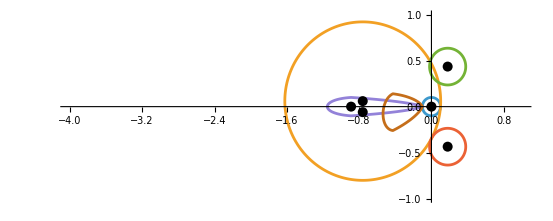

```mathematica
Show[
ParametricPlot[{ReIm[UPath6[t]], ReIm[UPath2[t]], ReIm[UPath4[t]],ReIm[UPath3[t]],ReIm[UPathB[t]],ReIm[UPath1[t]]},{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@U0]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6'[t]*matA1[l0,UPath6[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->60,MaxSteps->100000];
Non6=Psi[1]/.First[sol];
```

```mathematica
(* now with Richardson sum *)
F1dPeriodsN[λ_,u_,Nn_,Nr_]:=Module[{om1tab,om2tab,om1resum, om2resum,k,l},
om1tab=Table[u^n  Sum[k=n-2l;-(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) ,{l,0,Floor[n/2]}],{n,0,Nn}];
om2tab=Table[u^n Sum[k=n-2l; λ^(-k+l)(- If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 l! Gamma[1+k]^2),0]+- If[k<=l&&k+2l>0,( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k!)^2 l! Gamma[1-k+l]),0]),{l,0,Floor[n/2]}],{n,0,Nn}];
om1resum=RichardsonResum[Accumulate[om1tab],Nr];
om2resum=RichardsonResum[Accumulate[om2tab],Nr];
(*{(om2resum-1/4 (8 Log[1/ut]+Log[λ]) om1resum)/om1resum/(2Pi I)}*)
{om1resum,om2resum-1/4 (8 Log[u]+Log[λ]) om1resum}
];
F1PeriodsN[λ_,u_,Nn_,Nr_]:=Module[{varpi2tab,varpi3tab,varpi2resum,varpi3resum,varpi2,varpi3,k,l},
varpi2tab=Table[u^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3tab=Table[u^n Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
0 (-2 Log[u]-1/4 Log[λ])(k+2l)!/((l)!(k!)^2(l-k)!)/(k+2l)
+(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2resum=RichardsonResum[Accumulate[varpi2tab],Nr];
varpi3resum=RichardsonResum[Accumulate[varpi3tab],Nr];
(* replace ut by -ut in argument of Log !! *)
varpi2=Log[u]+varpi2resum;
varpi3=Log[u] ^2+(Log[u]+varpi2resum)(-2Log[u]-1/4 Log[λ])+Log[λ]^2/8+varpi3resum;
(*{varpi2,-4(varpi3)/(2Pi I)^2+1/6}*)
{varpi2,varpi3}
 ];
```

```mathematica
Simplify[F1PeriodsN[U l^(1/3),l^(1/3),4,0]]
```

{1/2 l (4+2 U+3 l U^2)+Log[l]/3,1/576 (-(-9+16 U-36 U^2+72 (2+3 l) U^3+1440 l U^4+576 l U^5+1872 l^2 U^6)/U^4-64 Log[l]^2-72 l (4+2 U+3 l U^2) Log[l^(1/3) U]+72 Log[l^(1/3) U]^2-48 Log[l] (4 l (4+2 U+3 l U^2)+Log[l^(1/3) U]))}

```mathematica
Series[2Pi I PiVec[[1]], {U,0,4}]
```

1+2 U^2+6 U^3+6 U^4+O[U]^5

```mathematica
-1-6 u^3-2 u^2 λ-6 u^4 λ^2/.{u->U l^(1/3),λ->l^(1/3)}/.{l->1}
```

-1-2 U^2-6 U^3-6 U^4

```mathematica
F1PeriodsN[1,]
```